# Complexité algorithmique des suites binaires courtes.

```mathematica
Package préliminaire, à activer une seule fois pour toutes :
```

```mathematica
MachineTable[S_,nb_]:=Grid[Partition[Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,2])/4,Mod[(#-Mod[#,2])/2,2],Mod[#,2]}≡#&/@PadLeft[IntegerDigits[nb,4S ],2S ])],2],Frame->All];
```

```mathematica
FigureFromTriple[{σ_,κ_,δ_}]:=4σ + 2 κ + δ;
```

```mathematica
ChangeNumbering[S_,number_]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,4S ],2S ],2]]],4S ];
```

```mathematica
SBTM[S_,nb_,limit_]:=Module[{tm},{tm=TuringMachine[{ChangeNumbering[S,nb],S,2},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[S,nb],S,2},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{S,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/S(tm11[[i]]-1)],{i,step+1}]}]};f[nb]];
```

```mathematica
rules[S_]:=Table[Thread[Thread[Partition[Flatten[Permutations[Partition[Range[4S-1,4,-1],4]]],4S-4]->Table[Range[4S-1,4,-1],{(S-1)!}]][[k]]],{k,(S-1)!}];
```

```mathematica
symS[nb_,S_]:=Module[{},{u=Partition[PadLeft[IntegerDigits[nb,4S],2S],2]};FromDigits[#,4S]&/@MapThread[ReplaceAll,{Partition[Flatten[    Map[Append[#,Last[u]]&,   (Permute[    Most[u],#]& /@Permutations[Range[S-1]])      ]],2S],rules[S]  }]];
```

## 1. Ordre naturel des suites binaires et numéro d’ordre d’une suite.

```mathematica
list[n_]:=PadLeft[IntegerDigits[Floor[n-2^Floor[Log[2,n]]],2], Floor[Log[2,n]]]
```

```mathematica
Table[Subscript[s, n]->list[n],{n,19}]
```

{s_1→{},s_2→{0},s_3→{1},s_4→{0,0},s_5→{0,1},s_6→{1,0},s_7→{1,1},s_8→{0,0,0},s_9→{0,0,1},s_10→{0,1,0},s_11→{0,1,1},s_12→{1,0,0},s_13→{1,0,1},s_14→{1,1,0},s_15→{1,1,1},s_16→{0,0,0,0},s_17→{0,0,0,1},s_18→{0,0,1,0},s_19→{0,0,1,1}}

```mathematica
number[suite_]:=FromDigits[Prepend[suite,1],2]      (*To decode, prepend the sequence with 1 and read the binary integer*)
```

```mathematica
number[{0,0,1,1}]
```

19

## 2. Complexité algorithmique d’une suite, s. Tout programme qui s’arrête imprime une suite traduisible en binaire. Parmi tous les programmes qui impriment s, il en est fatalement un qui est plus court que les autres. La complexité de s, K(s), vaut la longueur de ce programme minimum. K ne dépend du langage de programmation retenu qu’à une constante addititive inessentielle près. Afin de minimiser cette constante, il semble naturel de retenir le langage maximalement concis des machines de Turing à deux caractères (0 et 1) et S états (S>1) sans instruction explicite d’arrêt (Simple binary Turing machines, en abrégé SBTM).

## 3. Architecture des SBTM (due à Wolfram). Toute SBTM à S états (S ∈ {2, 3, 4, ... }), possède les attributs suivants : - Une bande semi-infinie (conventionnellement) vers la gauche est partitionnée en cellules. Chaque cellule est blanche ou noire selon qu’y est inscrit le caractère “0” ou “1”. La bande est (conventionnellement) initialement intégralement blanche (= peuplée de “0”). - Une tête de lecture-écriture est initialement positionnée en face de la cellule située à l’extrême droite de la bande. Cette tête est à tout instant dans un état, σ, défini parmi S états possibles, σ ∈ {0, 1, 2, ..., S-1}. La tête est initialement (conventionnellement) dans l’état, σ = 0. La machine fonctionne par pas discrets successifs en respectant une table comportant 2S instructions du type, (σ_old, κ_old) → (σ_new, κ_new, δ), (σ_old, σ_new ∈ {0, 1, 2, ..., S-1} et κ_old, κ_new, δ ∈ {0, 1}). A chaque pas, la tête lit le caractère, κ_old, situé en face d’elle et en fonction de son état interne, σ_old, effectue trois manoeuvres : - remplace κ_old par κ_new, - change l’état σ_old en σ_new, - se déplace d’une cellule vers la gauche (si δ=0) ou vers la droite (si δ=1). Une SBTM ne comporte aucun état explicite d’arrêt : elle s’arrête de fonctionner dès que la tête tente de déborder la cellule située à l’extrême droite de la bande donc de pénétrer la zone interdite (franchir la ligne rouge sur la figure suivante). Lorsque la machine s’arrête, elle imprime le résultat, lu (conventionnellement) de gauche à droite au départ de la cellule la plus à gauche jamais atteinte par la tête.

## 3.1. Structure ordonnée de la table d’instructions. Les instructions, (σ_old, κ_old) → (σ_new, κ_new, δ), sont du type, doublet→triplet. Les doublets sont en nombre 2S et les triplets en nombre 4S. Les triplets, t_i, sont numérotables dans l’ordre naturel : {0,0,0} ≡ 0, {0,0,1} ≡ 1, {0,1,0} ≡ 2, {0,1,1} ≡ 3, {1,0,0} ≡ 4, ..., {S-1,1,1} ≡ 4S-1. Tout triplet peut donc être codé par un chiffre en base 4S. On ordonne invariablement les doublets, donc aussi les intructions, dans l’ordre décroissant des états et des caractères : {{S-1,1} → t_1 , {S-1,0} → t_2 , {S-2,1} → t_3 , {S-2,0} → t_4 , ..., {0,1} → t_(2S-1) , {0,0} → t_(2S) }

## 3.2. Numérotation des SBTM à S états. L’adoption d’un ordre des doublets permet la numérotation des SBTM : toute SBTM est univoquement caractérisée par la suite ordonnée de ses triplets donc des chiffres associés, en base 4S. L’entier en base 4S, t_1t_2t_3t_4...t_(2S-1)t_(2S), est le numéro d’ordre de la machine (que l’on traduit en décimal pour plus de lisibilité). Remarque. Le design des machines simples de Turing est dû à Wolfram. Nous n’avons pas suivi les conventions peu naturelles adoptées par cet auteur : l’ordre dans lequel il considère les doublets, (σ_old, κ_old), dans la table d’instructions, la numérotation des états de 1 à S (au lieu de 0 à S-1) et le choix, δ ∈ {-1, 1} (au lieu de {0,1}). Il en résulte que sa numérotation diffère de la nôtre. L’instruction ChangeNumbering[S,nb] permet heureusement de passer d’une numérotation à l’autre et elle fonctionne dans les deux sens. Moyennant cette précaution, l’instruction TuringMachine, telle qu’implémentée dans Mathematica, fonctionne parfaitement.

## 3.3. Numérotation des SBTM tous états confondus. Il existe (4S)^(2S) SBTM à S états; ce nombre explose rapidement :

```mathematica
Grid[Table[{s,(4s )^(2s)},{s,2,7}]]
```

2 | 4096
3 | 2985984
4 | 4294967296
5 | 10240000000000
6 | 36520347436056576
7 | 182059119829942534144

## Les machines à deux états pourraient être numérotées de 0 à 4095, les machines à trois états de 4096 à 2990079, etc, mais on préfère garder la lisibilité du nombre des états en numérotant chaque famille de 0 à (4S)^(2S)-1.

## 4. L’exemple de la machine à 4 états n° 21944952. Cette machine s’arrête après 13 pas d’exécution et elle imprime la suite {0,1,0,0,1}. Légende : la ligne rouge limite la bande de lecture-écriture (la machine s’arrête lorsque la tête est invitée à la franchir) et les flèches oranges pointant sur l’heure, H, indiquent que la tête est momentanément dans l’état, σ = SH/12) :

```mathematica
MachineTable[4,21944952]        (* En base 4S=16, 21944952 se note 0 1 4 14 13 10 7 8 *)
```

{3,1}→{0,0,0}≡0 | {3,0}→{0,0,1}≡1
{2,1}→{1,0,0}≡4 | {2,0}→{3,1,0}≡14
{1,1}→{3,0,1}≡13 | {1,0}→{2,1,0}≡10
{0,1}→{1,1,1}≡7 | {0,0}→{2,0,0}≡8

```mathematica
SBTM[4,21944952,20]        (* 20 pas d'évolution ont été demandés mais l'arrêt se produit avant *)
```

-Graphics-

## 5. Doublets activés et machines équivalentes. Le premier doublet activé est toujours le dernier, {0,0}. Dans l’exemple précédent, ont été activés ensuite {2,0} puis {3,0}, etc. On note que le doublet, d_1=(3, 1), n’est jamais activé. Il en résulte que les 4S=16 machines caractérisées par les triplets {*,1,4,14,13,10,7,8} (où * peut être n’importe quel chiffre en base 4S=16) effectuent exactement la même tâche :

```mathematica
SBTM[4,#,13]&/@Table[FromDigits[{k,1,4,14,13,10,7,8},16],{k,0,15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 6. Machines équivalentes par symétries d’états. Mis à part l’état 0 qui est imposé au démarrage, les autres états peuvent être permutés sans qu’il en résulte un calcul différent au niveau de la bande. Lorsque S>2, (S-1)! machines (parfois un sous-multiple) sont équivalentes à une permutation près des états 1 à S-1. Dans l’exemple, on trouve 6 machines symétriques sur les états :

```mathematica
SBTM[4,#,13]&/@symS[21944952,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 7. Il existe une infinité de machines capables d’imprimer une suite donnée. L’exemple trivial est celui d’une machine à écrire qui se contente d’écrire la suite lors de déplacements successifs de la tête vers la gauche puis de repartir en sens inverse jusqu’à l’arrêt sans plus toucher au contenu de la bande.

```mathematica
nbprinter[s_]:=Join[{3+4 Length[s],1+4 Length[s],RandomInteger[4Length[s]+3],1+4 Length[s]+2 s⟦1⟧},Flatten[Table[{RandomInteger[4Length[s]+3],FigureFromTriple[{j,s[[Length[s]+1-j]],0}]},{j,Length[s]-1,1,-1}]]];
SBTM[6,FromDigits[nbprinter[{0,1, 0,0,1}],24],11]
```

-Graphics-

## 8. Profondeur logique d’une SBTM. Toute SBTM qui finit par s’arrêter en imprimant une suite, s, de longueur, N, a nécessairement subi un nombre impair, npas, de pas d’évolution. On définit la profondeusr logique de ce calcul par la relation : λ=(npas+1)/2. On a toujours l’inégalité, npas⩾2N-1, l’égalité prévalant dans le cas d’une machine à écrire. On peut aussi écrire : λ⩾N.

## 9. L’évolution de n’importe quelle machine est complètement décrite par un réel, ρ, compris entre 0 et 1. Ce nombre s’obtient en écrivant à la suite du point “décimal” les chiffres (en base 4S !) correspondant aux triplets successivement activés par la machine. Ce réel peut être traduit en notation décimale pour plus de commodité. Tous les réels compris entre 0 et 1 ne codent pas l’évolution d’une SBTM puisque, contrairement aux SBTM, ces réels sont en infinité non dénombrable. Un cas est cependant facile à régler : les rationnels au développement limité correspondent aux machines qui s’arrêtent tandis que les rationnels illimités correspondent aux machines qui bouclent périodiquement.

## 10. Comportements évolutifs des SBTM. Toute SBTM présente un des quatre comportements suivants : - limité (elle finit par s’arrêter), - périodique (elle finit par boucler, sa tête dérivant vers l’infini ou oscillant sur une portion limitée de la bande), - autosimilaire (elle finit par boucler, sa tête allant et venant avec des mouvements d’amplitudes variables mais structurés), - quelconque. Les machines à S=2, 3 ou 4 états ne présentent que les trois premiers types. A partir de S=5, rien n’est sûr même si l’on pense que cela reste le cas. "" | "S = 2" | "S = 3" | "S = 4" | "S = 5" "Total" | 4096 | 2985984 | 4294967296 | 10240000000000 "Halting (classe 1)" | 2347 "(57.3%)" | 1825642 "(61.1%)" | 2737817414 "(63.7%)" | "???" "Looping (classe 2)" | 1747 "(42.6%)" | 1159100 "(38.8%)" | 1555613138 "(36.2%)" | "???" "Nesting (classe 3)" | 2 "(4.8 10^-4)" | 1242 "(4.2 10^-4)" | 1536744 "(3.6 10^-4)" | "???" "Others (classe 4)" | 0 | 0 | 0 | "???" L’existence d’une classe 4 non vide est une conséquence de l’indécidabilité de l’arrêt des machines de Turing. Les machines à 2, 3 et 4 états sont donc toutes décidables au plan de l’arrêt.

## 11. Castors productifs et affairés. Les machines à 2, 3 et 4 états étant décidables, il vaut la peine d’attendre qu’elles manifestent toutes leur comportement ultime (arrêt, bouclage, auto similarité). Pour chaque valeur de S, une machine au moins est la plus productive (elle imprime la plus longue suite) et une machine au moins (pas forcément différente) calcule pendant le plus grand nombre de pas (sa profondeur logique est maximum). Lorsque S=2, la machine n° 486 est à la fois la plus féconde et la plus active (Elle n’est pas seule). Lorsque S=3, la machine n° 246582 est la plus féconde et la machine n°391096 est la plus active. Lorsque S=4, la machine n° 1183050430 est à la fois la plus féconde et la plus active. On a le tableau suivant (cfr §12 pour la dernière ligne) : "" | "S = 2" | "S = 3" | "S = 4" | "S = 5" "Greatest activity, C(S)" | 7 "steps" | 25 "steps" | 161 "steps" | "???" "Longest printed result, Γ(S)" | 3 "bits" | 6 "bits" | 20 "bits" | "???" "Elegant machines" | 8 | 31 | 283 | "???"

```mathematica
{SBTM[2,486,7],SBTM[3,246582,17],SBTM[3,391096,17],SBTM[4,1183050430,161]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 12. Machines élégantes. Lorsqu’on lance, dans l’ordre, les machines à 2 états (puis à 3 états, puis à 4 états), en ne retenant que celles qui s’arrêtent, on constate que la plupart impriment des suites déjà imprimées par une machine antérieure. Une machine qui imprime une suite pour la première fois est dite élégante (au sens de Chaitin). Le tableau précédent révèle que 8 machines à 2 états sont élégantes, de même, 31 machines à 3 états et 283 machines à 4 états. Voyons le cas des 8 machines à 2 états :

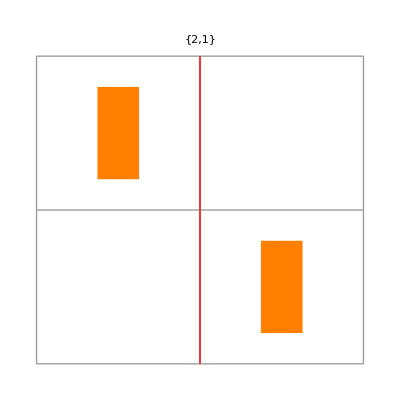
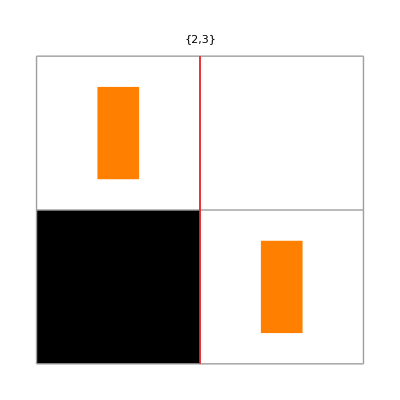
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{SBTM[2,1,10], SBTM[2,3,10], SBTM[2,78,10], SBTM[2,94,10], SBTM[2,206,10], SBTM[2,222,10], SBTM[2,486,10], SBTM[2,3308,10]}
```

## On voit apparaître la possibilité de réordonner l’ensemble des suites binaires dans l’ordre de production par les machines élégantes à 2, puis à 3 puis à 4 états, etc. Si on se limite à S=4, on trouve 8+31+283=322 suites rangées dans un ordre de complexité croissante. La complexité algorithmique d’une suite vaut, à présent, le nombre de chiffres binaires significatifs nécessaires pour écrire le numéro d’ordre de sa machine élégante, nb(s), celle qui l’a imprimée en premier lieu (Formellement : K(s)=Floor[Log[2,nb(s)+1]]) :

```mathematica
Length[s234]
```

322

```mathematica
Position[s234,{0}]
```

{{1}}

```mathematica
Table[1,{5}]
```

{1,1,1,1,1}

```mathematica
Position[s234,#]&/@Table[Table[1,{k}],{k,15}]
```

{{{2}},{{6}},{{7}},{{15}},{{21}},{{25}},{{62}},{{70}},{{61}},{{100}},{{129}},{{282}},{{231}},{{321}},{{130}}}

```mathematica
nbs1111={2,6,7,15,21,25,62,70,61,100,129,282,231,321,130,647,879,261,686,290,1124,1163,896,895,662,974,1171,1186,1812}
```

{2,6,7,15,21,25,62,70,61,100,129,282,231,321,130,647,879,261,686,290,1124,1163,896,895,662,974,1171,1186,1812}

```mathematica
Transpose[{Table[Table[1,{k}],{k,29}],Floor[Log[2,1+#]]&/@{2,6,7,15,21,25,62,70,61,100,129,282,231,321,130,647,879,261,686,290,1124,1163,896,895,662,974,1171,1186,1812}}]
```

{{{1},1},{{1,1},2},{{1,1,1},3},{{1,1,1,1},4},{{1,1,1,1,1},4},{{1,1,1,1,1,1},4},{{1,1,1,1,1,1,1},5},{{1,1,1,1,1,1,1,1},6},{{1,1,1,1,1,1,1,1,1},5},{{1,1,1,1,1,1,1,1,1,1},6},{{1,1,1,1,1,1,1,1,1,1,1},7},{{1,1,1,1,1,1,1,1,1,1,1,1},8},{{1,1,1,1,1,1,1,1,1,1,1,1,1},7},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1},8},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},7},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},9},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},9},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},8},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},9},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},8},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},9},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},9},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},9},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},9},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},10},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},10}}

```mathematica
HoldForm[1^#]&/@Table[k,{k,29}]
```

{1^1,1^2,1^3,1^4,1^5,1^6,1^7,1^8,1^9,1^10,1^11,1^12,1^13,1^14,1^15,1^16,1^17,1^18,1^19,1^20,1^21,1^22,1^23,1^24,1^25,1^26,1^27,1^28,1^29}

```mathematica
Transpose[{HoldForm[{1}^#]&/@Table[k,{k,29}],Floor[Log[2,1+#]]&/@{2,6,7,15,21,25,62,70,61,100,129,282,231,321,130,647,879,261,686,290,1124,1163,896,895,662,974,1171,1186,1812}}]
```

{{{1}^1,1},{{1}^2,2},{{1}^3,3},{{1}^4,4},{{1}^5,4},{{1}^6,4},{{1}^7,5},{{1}^8,6},{{1}^9,5},{{1}^10,6},{{1}^11,7},{{1}^12,8},{{1}^13,7},{{1}^14,8},{{1}^15,7},{{1}^16,9},{{1}^17,9},{{1}^18,8},{{1}^19,9},{{1}^20,8},{{1}^21,10},{{1}^22,10},{{1}^23,9},{{1}^24,9},{{1}^25,9},{{1}^26,9},{{1}^27,10},{{1}^28,10},{{1}^29,10}}

```mathematica
s234=#[[1]]&/@ElegantSBTM
```

```mathematica
{{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1},{0,0,0},{0,1,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{1,1,1,1},{1,0,1,0,1},{1,0,0,0},{1,1,1,0},{1,1,0,1},{0,0,0,1},{1,1,1,1,1},{0,1,0,1},{0,0,0,0},{0,1,1,1},{1,1,1,1,1,1},{1,0,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,0},{1,1,0,1,0,1},{1,1,0,0},{1,1,0,0,1},{1,0,0,1,1},{0,1,0,0},{0,1,1,0},{0,0,1,1},{1,0,1,1,1,1},{1,1,1,1,0},{1,1,0,0,0},{0,0,1,0},{1,0,0,0,0},{1,0,0,1,0},{1,0,1,1,0},{0,1,0,1,0},{0,1,1,1,1},{0,0,1,0,0},{1,0,1,1,0,1},{0,1,0,1,0,1},{0,1,0,0,1},{0,1,1,0,1},{0,0,0,0,1},{0,1,0,1,1},{0,1,0,0,0},{0,0,1,1,1},{1,0,1,1,1},{1,1,0,1,1},{1,1,1,0,1},{1,0,1,0,0},{1,1,1,1,1,0},{1,1,0,1,0},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,0,1,0,1,0},{0,1,1,1,0},{1,1,1,0,0},{1,0,1,0,1,0,1},{1,0,0,0,0,0},{0,0,0,1,1},{1,1,1,1,0,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,0},{1,0,1,0,1,0,1,0},{0,0,0,0,0},{0,1,1,0,1,1},{1,1,0,1,1,0},{1,1,1,1,1,1,1,1,0},{1,0,0,1,0,0,1},{0,0,1,1,0,1},{1,1,0,0,0,0,0},{1,0,1,1,1,1,1},{1,0,0,1,0,0,0,1,0,0},{1,1,0,1,1,0,1},{1,1,0,0,0,0},{1,0,0,0,0,1},{1,1,0,1,1,1},{1,0,1,1,0,0},{1,0,0,1,1,1},{1,0,0,1,0,0},{1,0,1,0,0,0},{1,0,1,0,1,1},{0,1,0,0,1,0},{0,0,0,1,0},{1,0,0,0,0,1,1},{0,0,1,0,0,0},{0,0,1,0,1},{0,0,1,1,0},{1,1,1,0,1,0,1},{1,1,1,0,0,0},{0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,0,0,1,0,1},{0,1,0,1,1,1},{0,1,1,1,1,1},{0,0,1,1,1,1},{1,0,1,1,1,0},{1,1,0,0,0,1},{1,0,1,0,0,1},{1,1,0,1,1,0,1,1},{1,1,1,1,1,1,1,0},{1,0,0,0,1,0,0},{1,0,0,0,1,1},{0,1,1,0,0},{0,1,0,1,0,1,0},{1,1,0,0,1,0},{1,1,1,1,1,0,1},{0,1,1,1,0,1},{1,0,1,0,1,0,1,0,1,0,1,1,1},{1,1,0,0,0,0,1,1},{0,0,0,0,1,1},{0,0,0,0,0,1},{0,1,0,0,0,0},{1,1,1,1,0,0},{1,1,1,1,0,1,1},{1,1,1,1,0,0,1},{1,0,0,0,0,1,0},{0,0,0,0,1,0},{1,0,1,0,1,0,1,0,1},{1,0,0,0,1,0},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,0,1,1,1,1},{1,1,0,0,0,0,1},{1,0,1,1,1,1,1,1,1},{1,0,1,1,0,1,1},{1,1,1,0,1,1},{1,1,1,0,1,1,1},{1,1,1,1,0,0,0},{1,1,1,0,0,1},{1,1,1,1,0,0,1,1},{1,0,1,1,1,0,1},{1,0,0,1,0,1,0},{1,0,1,1,1,1,0},{1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0},{0,0,0,1,0,0},{0,0,1,1,1,1,1},{1,0,0,0,1,1,1},{1,0,0,1,1,1,1},{0,0,1,0,1,1},{0,0,0,0,0,0},{1,0,0,1,1,0,1},{1,0,1,1,1,0,0},{1,0,0,1,1,0,0},{1,0,0,1,0,0,0},{1,0,0,0,0,0,1},{1,0,0,0,0,1,0,1,1},{1,0,1,1,0,0,1},{1,0,0,0,0,0,0,0,0,1},{1,1,0,1,0,1,1},{1,1,0,1,0,1,1,1,1},{1,0,0,0,1,0,1,1},{1,1,0,1,0,0,1,1},{1,0,1,1,0,1,0,1,0,1,0,1,0,1},{1,0,0,1,1,0,1,0},{0,1,0,0,0,1},{0,1,0,1,1,0},{1,1,0,0,1,0,1},{1,1,0,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,1,0,1,0},{1,0,0,1,1,0},{1,0,1,0,0,0,0},{1,0,1,1,0,1,0},{1,1,0,0,1,1,1},{1,0,1,0,0,1,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,1,1,0,0,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,0,1,0},{1,0,1,0,1,0,1,1,1,1},{0,1,0,1,0,1,0,1},{1,0,1,0,1,0,0},{1,0,1,0,1,1,0},{1,1,0,0,1,1},{0,1,0,0,1,0,0},{1,0,0,1,0,1,0,1,0},{1,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0},{1,1,1,1,0,1,0},{1,0,1,0,1,0,1,0,1,0},{1,0,0,0,1,0,0,0},{0,1,0,0,1,1},{1,1,0,0,1,0,0},{1,0,1,0,1,0,1,0,1,0,1},{1,1,0,1,0,0},{1,0,0,1,1,0,1,0,0},{1,1,0,1,0,1,0},{1,1,1,0,0,1,0},{1,0,0,1,1,1,0},{1,1,1,0,0,0,1},{1,0,0,0,1,0,1},{1,1,0,1,1,1,0},{1,1,0,0,1,0,0,1},{1,1,0,1,0,0,0},{1,0,0,0,0,0,0,1},{1,1,1,1,1,0,0},{1,0,1,0,0,1,0,0,1},{1,0,1,1,0,1,0,0,1},{1,1,0,0,0,1,1},{1,1,0,0,1,1,0,0,1},{1,1,0,0,1,0,0,1,1},{1,0,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,0,0,1,0,0,0,0},{1,0,0,1,0,1,0,1},{1,0,0,0,0,0,0,0,1},{0,1,1,0,1,0},{1,0,0,1,1,0,0,1},{1,1,1,1,1,1,0,1},{1,0,1,1,1,0,1,1},{1,0,0,0,1,1,1,1},{1,0,0,1,1,1,1,1},{1,0,0,1,0,0,0,0,0,0},{1,1,1,0,1,1,0},{1,0,0,0,1,0,0,1},{1,0,1,0,1,0,1,0,1,0,1,0,1},{0,0,0,0,0,0,0},{1,1,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,0,1},{0,1,1,0,0,1},{1,1,1,1,0,0,0,0},{1,1,1,1,1,1,1,1,1,0,1},{1,0,1,1,1,1,0,1},{0,1,1,1,1,0},{0,1,1,1,0,0},{1,0,1,0,1,1,1},{1,1,0,1,1,1,1,0},{1,0,1,0,1,0,1,1},{0,1,1,1,1,0,1},{0,1,1,0,1,1,0},{1,1,0,1,1,0,1,1,0},{1,1,0,1,0,1,0,1},{1,1,1,1,0,1,1,1,1,1},{1,1,1,1,0,1,1,0},{1,0,1,0,1,1,1,1},{1,0,1,0,0,1,0,0},{1,1,0,1,0,1,0,1,0},{1,0,1,1,0,1,1,0},{0,1,1,1,1,1,1},{0,1,0,1,1,0,1},{1,1,0,1,1,0,1,0},{1,1,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0},{0,1,1,1,1,1,0},{0,1,0,1,1,1,1},{0,0,1,1,0,0},{0,0,1,1,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,1,0,0,1},{1,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,1,0,1,0,1,0},{0,1,0,0,0,0,0},{1,1,1,1,0,0,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,0},{0,0,1,1,0,1,1},{1,0,1,1,0,1,1,0,1},{1,1,1,1,1,1,1,1,1,0},{1,0,1,0,0,0,0,0},{1,1,1,0,0,0,0,0},{0,0,0,0,0,1,1},{0,1,0,1,1,1,0},{1,1,1,0,1,1,1,0},{1,1,0,0,0,1,1,0},{1,1,1,0,0,0,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,1,1,0,1,1,0,1,1},{0,1,1,1,1,1,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,0},{0,0,0,0,0,0,1},{1,1,0,1,1,0,1,1,0,1,1},{1,0,1,0,1,0,0,1},{1,1,1,1,0,1,1,1,0,1},{1,0,1,1,1,1,1,0},{1,1,0,0,1,1,0,0,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,0,1,0,1,0,1,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,1,0,1,0,1},{1,0,1,0,0,0,0,1},{1,0,0,1,0,1,1},{1,0,1,1,0,1,0,1},{1,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,1,1,1,1,1,1,0,1},{1,1,0,0,1,1,0,0},{1,1,1,0,1,0,1,1},{1,1,1,0,1,1,0,0},{1,1,1,0,0,0,0},{0,1,0,1,0,1,1},{1,0,1,0,1,1,0,1},{1,1,0,0,1,0,1,0},{0,1,1,0,0,0},{1,1,1,1,1,0,1,0},{1,1,0,0,0,1,1,0,1,1},{1,0,1,1,1,1,1,1,0},{0,0,0,0,1,0,1},{0,1,1,0,1,1,0,1,1},{1,1,1,1,1,0,0,1},{1,0,1,0,0,0,0,1,1},{1,1,1,0,1,1,0,1},{1,1,1,0,1,1,1,1},{0,1,0,0,1,0,1},{1,0,1,1,0,0,0},{1,0,0,1,0,0,1,1},{1,1,0,1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,1,0,0}}
```

## Deux machines sont de complexité 1 (bit), Quatre machines sont de complexité 2 (bits), Huit machines sont de complexité 3 (bits), etc ... . L’ordre élégant diffère d’autant plus de l’ordre naturel que l’on monte en complexité. On peut voir l’algorithme comme une compression sans perte par machines de Turing élégantes. Le taux de compression vaut N/K(s). Certaines suites (la majorité) ont un taux de compression proche de 1 voire légèrement inférieur (la suite a été dilatée !), ces suites sont aléatoires. Par exemple la suite {0,1,1,1,1} de longueur, N=5, est imprimée par la 45ème machine élégante d’où K({0,1,1,1,1})=5 car l’écriture binaire de 45 exige 5 bits significatifs. D’autres suites ont un taux de compression nettement supérieur à 1, ce sont les suites non aléatoires, structurées par un programme court, une SBTM. Par exemple la suite {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} de longueur, N=15, est imprimée par la 130ème machine élégante d’où K({1,1,1,1,1,1,1,1,1,1,1,1,1,1,1})=7 car l’écriture binaire de 130 exige 7 bits significatifs. Voyons le cas intéressant des suites uniquement composées de “1” : en prenant en considération les machines à 2, 3, 4 et les premières machines à 5 états et en se limitant aux 1936 premières machines élégantes, on trouve que les suites composées de k “1” (pour k allant de 1 à 29) sont imprimées par les machines de numéro d’ordre : {2,6,7,15,21,25,62,70,61,100,129,282,231,321,130,647,879,261,686,290,1124,1163,896,895,662,974,1171,1186,1812}. Notant ces suites sous la forme abrégée, {1}^k, voici les complexités correspondantes : {{{1}^1,1},{{1}^2,2},{{1}^3,3},{{1}^4,4},{{1}^5,4},{{1}^6,4},{{1}^7,5},{{1}^8,6},{{1}^9,5},{{1}^10,6},{{1}^11,7},{{1}^12,8},{{1}^13,7},{{1}^14,8},{{1}^15,7},{{1}^16,9},{{1}^17,9},{{1}^18,8},{{1}^19,9},{{1}^20,8},{{1}^21,10},{{1}^22,10},{{1}^23,9},{{1}^24,9},{{1}^25,9},{{1}^26,9},{{1}^27,10},{{1}^28,10},{{1}^29,10}}

## On voit que ces suites sont de moins en moins aléatoires. Il y a lieu de noter que la complexité de certaines suites du type {1}^k (k très grand) peuvent être de complexité beaucoup plus faibles que leurs voisines {1}^(k-1) et {1}^(k+1), c’est typiquement le cas de la suite correspondant au castor fertile à 5 états (k dépassant les 40000).

```mathematica
ElegantSBTM={{{0},1,1},{{1},3,1},{{0,0},78,2},{{0,1},94,2},{{1,0},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4},{{0,0,0},22194,3},{{0,1,1},22218,3},{{0,1,0},22312,3},{{0,0,1},27426,3},{{1,0,0},31648,4},{{1,1,0},31672,4},{{1,1,1,1},70210,7},{{1,0,1,0,1},70674,7},{{1,0,0,0},80658,5},{{1,1,1,0},80706,7},{{1,1,0,1},80752,7},{{0,0,0,1},93270,8},{{1,1,1,1,1},97882,7},{{0,1,0,1},124182,7},{{0,0,0,0},134696,7},{{0,1,1,1},237970,8},{{1,1,1,1,1,1},246582,9},{{1,0,0,0,1},319482,10},{{1,0,0,1},329562,7},{{1,0,1,1},329608,7},{{1,0,1,0},385316,7},{{1,1,0,1,0,1},391096,13},{{1,1,0,0},392176,7},{{1,1,0,0,1},392180,9},{{1,0,0,1,1},392204,8},{{0,1,0,0},945040,6},{{0,1,1,0},945064,6},{{0,0,1,1},1074620,9},{{1,0,1,1,1,1},1568804,10},{{1,1,1,1,0},1812450,11},{{1,1,0,0,0},2124286,12},{{0,0,1,0},6611802,9},{{1,0,0,0,0},16992982,7},{{1,0,0,1,0},17084248,7},{{1,0,1,1,0},17084280,7},{{0,1,0,1,0},17190648,9},{{0,1,1,1,1},17737782,7},{{0,0,1,0,0},20867732,9},{{1,0,1,1,0,1},21232248,14},{{0,1,0,1,0,1},21928566,11},{{0,1,0,0,1},21944952,7},{{0,1,1,0,1},21953144,7},{{0,0,0,0,1},23354936,16},{{0,1,0,1,1},24009272,11},{{0,1,0,0,0},24009336,7},{{0,0,1,1,1},24017492,8},{{1,0,1,1,1},24530746,10},{{1,1,0,1,1},25426548,14},{{1,1,1,0,1},25579450,14},{{1,0,1,0,0},25614186,8},{{1,1,1,1,1,0},50630230,12},{{1,1,0,1,0},50679446,10},{{1,1,1,1,1,1,1,1,1},51088454,19},{{1,1,1,1,1,1,1},51096710,17},{{1,0,1,0,1,0},51284694,8},{{0,1,1,1,0},52341908,13},{{1,1,1,0,0},52776598,11},{{1,0,1,0,1,0,1},54421716,11},{{1,0,0,0,0,0},54437910,9},{{0,0,0,1,1},54943688,13},{{1,1,1,1,0,1},54951512,12},{{1,1,1,1,1,1,1,1},54953838,15},{{1,1,1,1,1,1,0},54971992,16},{{1,0,1,0,1,0,1,0},55275226,16},{{0,0,0,0,0},55336552,13},{{0,1,1,0,1,1},55348602,13},{{1,1,0,1,1,0},55349082,14},{{1,1,1,1,1,1,1,1,0},55486614,22},{{1,0,0,1,0,0,1},55499350,10},{{0,0,1,1,0,1},56930136,13},{{1,1,0,0,0,0,0},57563764,11},{{1,0,1,1,1,1,1},57571924,10},{{1,0,0,1,0,0,0,1,0,0},59006886,36},{{1,1,0,1,1,0,1},59592374,14},{{1,1,0,0,0,0},60190392,10},{{1,0,0,0,0,1},61790324,13},{{1,1,0,1,1,1},62319768,15},{{1,0,1,1,0,0},68905566,11},{{1,0,0,1,1,1},68905628,8},{{1,0,0,1,0,0},68905630,8},{{1,0,1,0,0,0},70998638,11},{{1,0,1,0,1,1},70998726,12},{{0,1,0,0,1,0},73311128,11},{{0,0,0,1,0},73319320,12},{{1,0,0,0,0,1,1},76461914,18},{{0,0,1,0,0,0},76769822,11},{{0,0,1,0,1},77019790,9},{{0,0,1,1,0},78067870,10},{{1,1,1,0,1,0,1},78526296,10},{{1,1,1,0,0,0},78866974,11},{{0,0,0,1,1,1},80291726,14},{{1,1,1,1,1,1,1,1,1,1},82295532,19},{{1,0,0,1,0,1},83335788,12},{{0,1,0,1,1,1},83585692,15},{{0,1,1,1,1,1},86932068,9},{{0,0,1,1,1,1},93748904,14},{{1,0,1,1,1,0},95390598,14},{{1,1,0,0,0,1},101696404,16},{{1,0,1,0,0,1},101927550,16},{{1,1,0,1,1,0,1,1},102459580,17},{{1,1,1,1,1,1,1,0},102496334,25},{{1,0,0,0,1,0,0},102671256,12},{{1,0,0,0,1,1},102673276,10},{{0,1,1,0,0},104450740,7},{{0,1,0,1,0,1,0},104942268,17},{{1,1,0,0,1,0},105060956,11},{{1,1,1,1,1,0,1},106688428,20},{{0,1,1,1,0,1},108968360,9},{{1,0,1,0,1,0,1,0,1,0,1,1,1},109548462,59},{{1,1,0,0,0,0,1,1},110316158,28},{{0,0,0,0,1,1},110595916,16},{{0,0,0,0,0,1},110595918,17},{{0,1,0,0,0,0},111059384,9},{{1,1,1,1,0,0},111064972,12},{{1,1,1,1,0,1,1},111940472,10},{{1,1,1,1,0,0,1},111956856,10},{{1,0,0,0,0,1,0},115546716,11},{{0,0,0,0,1,0},115579604,14},{{1,0,1,0,1,0,1,0,1},115655514,18},{{1,0,0,0,1,0},115808852,9},{{1,1,1,1,1,1,1,1,1,1,1},117131438,31},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},117131470,48},{{1,1,0,1,1,1,1},117135566,12},{{1,1,0,0,0,0,1},117151950,14},{{1,0,1,1,1,1,1,1,1},124706698,18},{{1,0,1,1,0,1,1},126227418,17},{{1,1,1,0,1,1},126640038,9},{{1,1,1,0,1,1,1},126811450,14},{{1,1,1,1,0,0,0},127319720,12},{{1,1,1,0,0,1},128850132,14},{{1,1,1,1,0,0,1,1},128931948,18},{{1,0,1,1,1,0,1},129190614,16},{{1,0,0,1,0,1,0},133488296,18},{{1,0,1,1,1,1,0},134126150,18},{{1,0,0,0,0,0,0,0},223311978,18},{{1,0,0,0,0,0,0},223320170,15},{{0,0,0,1,0,0},224681866,15},{{0,0,1,1,1,1,1},258758830,20},{{1,0,0,0,1,1,1},279369560,14},{{1,0,0,1,1,1,1},279369592,14},{{0,0,1,0,1,1},294546298,21},{{0,0,0,0,0,0},307190376,12},{{1,0,0,1,1,0,1},312795000,18},{{1,0,1,1,1,0,0},312923976,15},{{1,0,0,1,1,0,0},312924024,14},{{1,0,0,1,0,0,0},312924056,15},{{1,0,0,0,0,0,1},323897526,16},{{1,0,0,0,0,1,0,1,1},325349112,42},{{1,0,1,1,0,0,1},325865082,23},{{1,0,0,0,0,0,0,0,0,1},325905012,35},{{1,1,0,1,0,1,1},326003444,10},{{1,1,0,1,0,1,1,1,1},328100596,15},{{1,0,0,0,1,0,1,1},328100730,36},{{1,1,0,1,0,0,1,1},329543512,45},{{1,0,1,1,0,1,0,1,0,1,0,1,0,1},329567960,42},{{1,0,0,1,1,0,1,0},330102870,19},{{0,1,0,0,0,1},330225780,16},{{0,1,0,1,1,0},330225782,14},{{1,1,0,0,1,0,1},330225784,15},{{1,1,0,1,1,1,1,1},330233972,19},{{1,0,1,1,1,1,1,1},339700412,19},{{1,1,1,0,1,0},341751720,12},{{1,0,0,1,1,0},342350526,8},{{1,0,1,0,0,0,0},342647770,17},{{1,0,1,1,0,1,0},342874740,16},{{1,1,0,0,1,1,1},344897370,11},{{1,0,1,0,0,1,0},345419708,12},{{0,1,0,1,0,0},345942968,14},{{0,0,1,0,1,0},345991772,25},{{0,0,0,1,0,1},345991934,11},{{1,1,1,0,0,1,1},346961880,11},{{1,1,1,1,1,0,1,1},347040444,32},{{1,1,1,1,1,1,1,0,1,0},348088924,52},{{1,0,1,0,1,0,1,1,1,1},348089084,39},{{0,1,0,1,0,1,0,1},349080442,24},{{1,0,1,0,1,0,0},350136216,18},{{1,0,1,0,1,1,0},351709112,22},{{1,1,0,0,1,1},352021054,9},{{0,1,0,0,1,0,0},372886228,23},{{1,0,0,1,0,1,0,1,0},373206940,16},{{1,0,0,1,0,1,0,0},374319260,16},{{1,0,0,1,0,0,1,0},374319262,14},{{1,1,1,1,0,1,0},374565628,22},{{1,0,1,0,1,0,1,0,1,0},375311272,24},{{1,0,0,0,1,0,0,0},376416476,19},{{0,1,0,0,1,1},378450298,12},{{1,1,0,0,1,0,0},378522324,14},{{1,0,1,0,1,0,1,0,1,0,1},378530548,26},{{1,1,0,1,0,0},379490204,12},{{1,0,0,1,1,0,1,0,0},379490236,20},{{1,1,0,1,0,1,0},380955640,19},{{1,1,1,0,0,1,0},382616536,14},{{1,0,0,1,1,1,0},383691576,12},{{1,1,1,0,0,0,1},383691608,16},{{1,0,0,0,1,0,1},383691768,13},{{1,1,0,1,1,1,0},384019196,12},{{1,1,0,0,1,0,0,1},384031352,17},{{1,1,0,1,0,0,0},384031484,13},{{1,0,0,0,0,0,0,1},384035448,21},{{1,1,1,1,1,0,0},384610196,19},{{1,0,1,0,0,1,0,0,1},384817780,21},{{1,0,1,1,0,1,0,0,1},385147800,29},{{1,1,0,0,0,1,1},385147832,31},{{1,1,0,0,1,1,0,0,1},385781660,23},{{1,1,0,0,1,0,0,1,1},394505972,29},{{1,0,1,1,0,1,1,1},395229942,29},{{1,1,1,1,0,1,1,1},397342868,21},{{1,1,0,0,1,0,0,0,0},491171640,29},{{1,0,0,1,0,1,0,1},523529882,16},{{1,0,0,0,0,0,0,0,1},525224630,25},{{0,1,1,0,1,0},525627066,12},{{1,0,0,1,1,0,0,1},527724186,22},{{1,1,1,1,1,1,0,1},529951800,25},{{1,0,1,1,1,0,1,1},531548246,17},{{1,0,0,0,1,1,1,1},531552340,15},{{1,0,0,1,1,1,1,1},531560532,15},{{1,0,0,1,0,0,0,0,0,0},595877798,35},{{1,1,1,0,1,1,0},618567624,17},{{1,0,0,0,1,0,0,1},647187068,17},{{1,0,1,0,1,0,1,0,1,0,1,0,1},648987480,30},{{0,0,0,0,0,0,0},795629742,13},{{1,1,0,1,1,0,0},827288276,16},{{1,1,1,1,1,1,1,1,1,1,1,1,1},860655226,44},{{0,0,1,0,0,1},883842888,19},{{0,1,1,0,0,1},883842904,11},{{1,1,1,1,0,0,0,0},888891934,18},{{1,1,1,1,1,1,1,1,1,0,1},888957784,64},{{1,0,1,1,1,1,0,1},900091752,35},{{0,1,1,1,1,0},900136568,9},{{0,1,1,1,0,0},900136664,12},{{1,0,1,0,1,1,1},910936222,19},{{1,1,0,1,1,1,1,0},911190166,17},{{1,0,1,0,1,0,1,1},912183208,21},{{0,1,1,1,1,0,1},915186046,24},{{0,1,1,0,1,1,0},915270324,18},{{1,1,0,1,1,0,1,1,0},915383198,27},{{1,1,0,1,0,1,0,1},915401436,17},{{1,1,1,1,0,1,1,1,1,1},917295992,20},{{1,1,1,1,0,1,1,0},917489560,23},{{1,0,1,0,1,1,1,1},918455188,17},{{1,0,1,0,0,1,0,0},920552340,17},{{1,1,0,1,0,1,0,1,0},921676500,16},{{1,0,1,1,0,1,1,0},922543000,18},{{0,1,1,1,1,1,1},922544458,27},{{0,1,0,1,1,0,1},922610324,13},{{1,1,0,1,1,0,1,0},922665944,22},{{1,1,0,0,0,0,0,0,0,1},927914630,31},{{1,1,0,0,0,0,0,0},936281450,22},{{0,1,1,1,1,1,0},1030638328,17},{{0,1,0,1,1,1,1},1030650456,13},{{0,0,1,1,0,0},1033661108,15},{{0,0,1,1,1,0},1034353784,14},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1066166964,60},{{0,1,0,0,1,0,0,1},1095686774,16},{{1,0,0,0,0,0,0,0,0,0,0},1099123414,30},{{0,1,0,1,0,1,0,1,0,1,0},1099411190,40},{{0,1,0,0,0,0,0},1100394168,12},{{1,1,1,1,0,0,1,0},1104112538,29},{{1,1,1,1,1,1,1,1,1,1,1,1,0},1129221270,44},{{0,0,1,1,0,1,1},1131338364,25},{{1,0,1,1,0,1,1,0,1},1131400854,23},{{1,1,1,1,1,1,1,1,1,0},1131859546,38},{{1,0,1,0,0,0,0,0},1132354204,17},{{1,1,1,0,0,0,0,0},1132354236,16},{{0,0,0,0,0,1,1},1133435580,20},{{0,1,0,1,1,1,0},1133436058,21},{{1,1,1,0,1,1,1,0},1133965240,27},{{1,1,0,0,0,1,1,0},1134455484,15},{{1,1,1,0,0,0,1,1},1134520508,16},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},1134997208,40},{{1,1,1,0,1,1,0,1,1},1135082584,49},{{0,1,1,1,1,1,1,1},1135447286,20},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},1136045784,57},{{1,1,1,1,1,1,1,1,1,1,1,1},1136117870,47},{{1,1,1,1,1,1,1,1,1,1,0},1137109850,50},{{0,0,0,0,0,0,1},1138142328,22},{{1,1,0,1,1,0,1,1,0,1,1},1138665660,27},{{1,0,1,0,1,0,0,1},1139595354,17},{{1,1,1,1,0,1,1,1,0,1},1140255896,30},{{1,0,1,1,1,1,1,0},1140755100,16},{{1,1,0,0,1,1,0,0,1,0},1183029854,24},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1183050430,81},{{1,0,1,0,1,0,1,0,1,0,0},1183765338,27},{{1,0,0,0,0,0,0,0,0},1184005100,21},{{1,0,0,0,1,0,1,0,1,0,1},1185698648,25},{{1,0,1,0,0,0,0,1},1185829880,15},{{1,0,0,1,0,1,1},1189321720,35},{{1,0,1,1,0,1,0,1},1189376856,15},{{1,0,0,0,0,0,0,0,0,0},1189901082,22},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},1190962008,56},{{1,1,1,1,1,1,1,1,0,1},1201916118,48},{{1,1,0,0,1,1,0,0},1216584286,18},{{1,1,1,0,1,0,1,1},1216584382,18},{{1,1,1,0,1,1,0,0},1233535962,25},{{1,1,1,0,0,0,0},1250123356,14},{{0,1,0,1,0,1,1},1250139326,21},{{1,0,1,0,1,1,0,1},1336828760,15},{{1,1,0,0,1,0,1,0},1401417902,26},{{0,1,1,0,0,0},1403975702,11},{{1,1,1,1,1,0,1,0},1415801564,27},{{1,1,0,0,0,1,1,0,1,1},1535550332,27},{{1,0,1,1,1,1,1,1,0},1603159034,26},{{0,0,0,0,1,0,1},1637763322,24},{{0,1,1,0,1,1,0,1,1},1644055224,18},{{1,1,1,1,1,0,0,1},1670274044,76},{{1,0,1,0,0,0,0,1,1},1671343220,21},{{1,1,1,0,1,1,0,1},1672432540,21},{{1,1,1,0,1,1,1,1},1673414812,17},{{0,1,0,0,1,0,1},1686330012,19},{{1,0,1,1,0,0,0},1786994428,17},{{1,0,0,1,0,0,1,1},1788232700,23},{{1,1,0,1,1,1,1,0,1,1,1},1939753718,56},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1},2055496636,73},{{0,0,0,0,1,0,0},3333313528,27}};
```

## 13. Problèmes liés à l’indécidabilité de l’arrêt des SBTM. L’arrêt (mais aussi la périodicité ou l’auto similarité) des machines de Turing est frappé d’indécidabilité générique. C’est un obstacle à la détermination de la complexité algorithmique des suites de plus en plus longues par des machines à un nombre croissant d’états. La seule startégie envisageable est de se limiter à un nombre de pas d’exécutions fixé d’avance et de passer à la machine suivante en cas d’indécision (temporaire ?). Ce faisant on ignore une machine qui se serait peut-être révélée élégante d’où une surestimation de la complexité des suites concernées.

## 14. Sauf le cas S=5 qui n’est pas loin d’une solution définitive allant probablement dans le sens d’une décidabilité de toutes ses machines, le problème de la reconnaissance des machines périodiques ou auto similaires posera un problème progressivement insoluble.